{-1,-0.96,-0.92,-0.88,-0.84,-0.8,-0.76,-0.72,-0.68,-0.64,-0.6,-0.56,-0.52,-0.48,-0.44,-0.4,-0.36,-0.32,-0.28,-0.24,-0.2,-0.16,-0.12,-0.08,-0.04,0,0.04,0.08,0.12,0.16,0.2,0.24,0.28,0.32,0.36,0.4,0.44,0.48,0.52,0.56,0.6,0.64,0.68,0.72,0.76,0.8,0.84,0.88,0.92,0.96,1}

-1

1

{0.0384615,0.0415973,0.0451264,0.0491159,0.0536481,0.0588235,0.0647668,0.0716332,0.0796178,0.088968,0.1,0.113122,0.128866,0.147929,0.171233,0.2,0.235849,0.280899,0.337838,0.409836,0.5,0.609756,0.735294,0.862069,0.961538,1,0.961538,0.862069,0.735294,0.609756,0.5,0.409836,0.337838,0.280899,0.235849,0.2,0.171233,0.147929,0.128866,0.113122,0.1,0.088968,0.0796178,0.0716332,0.0647668,0.0588235,0.0536481,0.0491159,0.0451264,0.0415973,0.0384615}

51

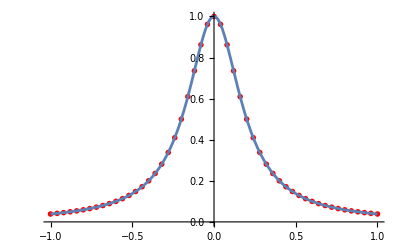

```mathematica
rData = Import["C:\\Users\\Alex\\Desktop\\labs3kurs\\Interpolation_results\\polyvalues5.txt", "table"];
X = rData[[2]]
a =X[[1]]
b=X[[-1]]
Y = rData[[4]]
m=rData[[1]][[2]]

(*Points=rData[[6]]
Coeffs=rData[[8]]
n=rData[[7]][[2]]*)
(*L[x_]:=Evaluate[Coeffs[[1]]+Sum[Coeffs[[i]]Product[(y-Points[[k]]),{k,1,i-1}],{i,2,n}]]/.y->x;*)
(*f[x_]:=(4 x^3+2 x^2−4x+2)^(√2)+ArcSin[1/(5+x-x^2)]-5;*)
f[x_]:=1/(1+25 x^2);
(*f[x_]:=1/ArcTan[1+10 x^2]*)
(*f[x_]:=Sin[π x];*)
Show[ListPlot[Table[{X[[i]],Y[[i]]},{i,m}],PlotStyle->{Red, PointSize[0.01]}](*,PlotRange->{{-1,1},{-2,2}}*),Plot[{f[x]},{x,a,b}]]
(*err1=Maximize[{Abs[L[x]-f[x]],a<=x<=b},x]
err2=MaximalBy[Table[{Abs[Y[[i]]-f[X[[i]]]],X[[i]]},{i,m}],First][[1]]*)
```

```mathematica
{-1,-0.96,-0.92,-0.88,-0.84,-0.8,-0.76,-0.72,-0.68,-0.64,-0.6,-0.56,-0.52,-0.48,-0.44,-0.4,-0.36,-0.32,-0.28,-0.24,-0.2,-0.16,-0.12,-0.08,-0.04,0,0.04,0.08,0.12,0.16,0.2,0.24,0.28,0.32,0.36,0.4,0.44,0.48,0.52,0.56,0.6,0.64,0.68,0.72,0.76,0.8,0.84,0.88,0.92,0.96,1}
```

-1

1

{-1.22465×10^-16,-4.70389×10^14,-5.01281×10^10,1.72439×10^7,109809,-81.1556,1.64482,-0.767,-0.844455,-0.904827,-0.951056,-0.982287,-0.998027,-0.998027,-0.982287,-0.951057,-0.904827,-0.844328,-0.770513,-0.684547,-0.587785,-0.481754,-0.368125,-0.24869,-0.125333,0,0.125333,0.24869,0.368125,0.481754,0.587785,0.684547,0.770513,0.844328,0.904827,0.951057,0.982287,0.998027,0.998027,0.982287,0.951057,0.904826,0.844407,0.772081,4.37249,381.851,80900.8,4.14185×10^7,6.74124×10^10,1.60126×10^15,1.22465×10^-16}

51

-Graphics-

```mathematica
f[0.98]
```

0.0627905

```mathematica
0.06279051952931358
0.0627905
0.0526038
```

0.0627905

0.0627905

0.0526038

```mathematica
D[f[x],{x,n+1}]
```

π^8 Sin[π x]

```mathematica
n
```

7

```mathematica
Y[[n]]
```

-0.55557

```mathematica
errT={0,0,0,0,0};
```

```mathematica
errT[[4]]=err2[[1]]
```

{-0.546875,4.90035×10^-7}

```mathematica
errT
```

{0,0,0,{-0.546875,4.90035×10^-7},0}

-1

1

{-1.22465×10^-16,-0.0490677,-0.0980171,-0.14673,-0.19509,-0.24298,-0.290285,-0.33689,-0.382683,-0.427555,-0.471397,-0.514103,-0.55557,-0.595699,-0.634393,-0.671559,-0.707107,-0.740951,-0.77301,-0.803208,-0.83147,-0.857729,-0.881921,-0.903989,-0.92388,-0.941544,-0.95694,-0.970031,-0.980785,-0.989177,-0.995185,-0.998795,-1,-0.998795,-0.995185,-0.989177,-0.980785,-0.970031,-0.95694,-0.941544,-0.92388,-0.903989,-0.881921,-0.857729,-0.83147,-0.803208,-0.77301,-0.740951,-0.707107,-0.671559,-0.634393,-0.595699,-0.55557,-0.514103,-0.471397,-0.427555,-0.382683,-0.33689,-0.290285,-0.24298,-0.19509,-0.14673,-0.0980171,-0.0490677,-2.22261×10^-18,0.0490677,0.0980171,0.14673,0.19509,0.24298,0.290285,0.33689,0.382683,0.427555,0.471397,0.514103,0.55557,0.595699,0.634393,0.671559,0.707107,0.740951,0.77301,0.803208,0.83147,0.857729,0.881921,0.903989,0.92388,0.941544,0.95694,0.970031,0.980785,0.989177,0.995185,0.998795,1,0.998795,0.995185,0.989177,0.980785,0.970031,0.95694,0.941544,0.92388,0.903989,0.881921,0.857729,0.83147,0.803208,0.77301,0.740951,0.707107,0.671559,0.634393,0.595699,0.55557,0.514103,0.471397,0.427555,0.382683,0.33689,0.290285,0.24298,0.19509,0.14673,0.0980171,0.0490677,1.24517×10^-16}

129

{-1,-0.984375,-0.96875,-0.953125,-0.9375,-0.921875,-0.90625,-0.890625,-0.875,-0.859375,-0.84375,-0.828125,-0.8125,-0.796875,-0.78125,-0.765625,-0.75,-0.734375,-0.71875,-0.703125,-0.6875,-0.671875,-0.65625,-0.640625,-0.625,-0.609375,-0.59375,-0.578125,-0.5625,-0.546875,-0.53125,-0.515625,-0.5,-0.484375,-0.46875,-0.453125,-0.4375,-0.421875,-0.40625,-0.390625,-0.375,-0.359375,-0.34375,-0.328125,-0.3125,-0.296875,-0.28125,-0.265625,-0.25,-0.234375,-0.21875,-0.203125,-0.1875,-0.171875,-0.15625,-0.140625,-0.125,-0.109375,-0.09375,-0.078125,-0.0625,-0.046875,-0.03125,-0.015625,0,0.015625,0.03125,0.046875,0.0625,0.078125,0.09375,0.109375,0.125,0.140625,0.15625,0.171875,0.1875,0.203125,0.21875,0.234375,0.25,0.265625,0.28125,0.296875,0.3125,0.328125,0.34375,0.359375,0.375,0.390625,0.40625,0.421875,0.4375,0.453125,0.46875,0.484375,0.5,0.515625,0.53125,0.546875,0.5625,0.578125,0.59375,0.609375,0.625,0.640625,0.65625,0.671875,0.6875,0.703125,0.71875,0.734375,0.75,0.765625,0.78125,0.796875,0.8125,0.828125,0.84375,0.859375,0.875,0.890625,0.90625,0.921875,0.9375,0.953125,0.96875,0.984375,1}

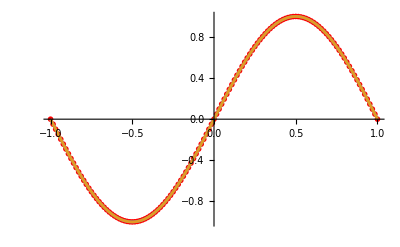

{5.37892×10^-7,{x→-0.28125}}

{{-0.546875,4.90035×10^-7},{-0.453125,4.90035×10^-7},{0.453125,4.90035×10^-7},{0.546875,4.90035×10^-7}}

```mathematica
rData2 = Import["C:\\Users\\Alex\\Desktop\\labs3kurs\\Interpolation_results\\splinevalues5.txt", "table"];
X2 = rData2[[2]];
a2 =X2[[1]]
b2=X2[[-1]]
Y2 = rData2[[4]]
m2=rData2[[1]][[2]]

Points2=rData2[[6]]
CoA=rData2[[8]];
CoB=rData2[[10]];
CoC=rData2[[12]];
CoD=rData2[[14]];
n2=rData2[[7]][[2]];
S[x_]:=Piecewise[Table[{CoA[[i]]+CoB[[i]](x-Points2[[i]])+CoC[[i]](x-Points2[[i]])^2+CoD[[i]](x-Points2[[i]])^3,Points2[[i]]<=x<=Points2[[i+1]]},{i,n2}],x];
(*f[x_]:=1/ArcTan[1+10 x^2];*)
(*f[x_]:=(4 x^3+2 x^2−4x+2)^(√2)+ArcSin[1/(5+x-x^2)]-5;
f[x_]:=1/(1+25 x^2);*)
(*f[x_]:=x^2;*)
f[x_]:=Sin[π x];
Show[ListPlot[Table[{X2[[i]],Y2[[i]]},{i,m2}],PlotStyle->{Red, PointSize[0.01]}],Plot[{f[x],S[x]},{x,a2,b2}]]
err1=Maximize[{Abs[S[x]-f[x]],a<=x<=b},x]
err2=MaximalBy[Table[{X2[[i]],Abs[Y2[[i]]-f[X2[[i]]]]},{i,m2}],Last]
```

```mathematica
S[x]
```

Piecewise[{{-1.22465×10^-16-3.14159 (1+x)+5.16668 (1+x)^3, -1≤x≤-0.984375}, {-0.0490677-3.13781 (0.984375+x)+0.242188 (0.984375+x)^2+5.15423 (0.984375+x)^3, -0.984375≤x≤-0.96875}, {-0.0980171-3.12646 (0.96875+x)+0.483792 (0.96875+x)^2+5.12936 (0.96875+x)^3, -0.96875≤x≤-0.953125}, {-0.14673-3.10759 (0.953125+x)+0.724231 (0.953125+x)^2+5.09214 (0.953125+x)^3, -0.953125≤x≤-0.9375}, {-0.19509-3.08123 (0.9375+x)+0.962925 (0.9375+x)^2+5.04265 (0.9375+x)^3, -0.9375≤x≤-0.921875}, {-0.24298-3.04744 (0.921875+x)+1.1993 (0.921875+x)^2+4.98102 (0.921875+x)^3, -0.921875≤x≤-0.90625}, {-0.290285-3.00632 (0.90625+x)+1.43279 (0.90625+x)^2+4.90738 (0.90625+x)^3, -0.90625≤x≤-0.890625}, {-0.33689-2.95795 (0.890625+x)+1.66282 (0.890625+x)^2+4.82192 (0.890625+x)^3, -0.890625≤x≤-0.875}, {-0.382683-2.90245 (0.875+x)+1.88885 (0.875+x)^2+4.72485 (0.875+x)^3, -0.875≤x≤-0.859375}, {-0.427555-2.83997 (0.859375+x)+2.11032 (0.859375+x)^2+4.61639 (0.859375+x)^3, -0.859375≤x≤-0.84375}, {-0.471397-2.77064 (0.84375+x)+2.32672 (0.84375+x)^2+4.49681 (0.84375+x)^3, -0.84375≤x≤-0.828125}, {-0.514103-2.69463 (0.828125+x)+2.5375 (0.828125+x)^2+4.3664 (0.828125+x)^3, -0.828125≤x≤-0.8125}, {-0.55557-2.61214 (0.8125+x)+2.74218 (0.8125+x)^2+4.22547 (0.8125+x)^3, -0.8125≤x≤-0.796875}, {-0.595699-2.52335 (0.796875+x)+2.94025 (0.796875+x)^2+4.07436 (0.796875+x)^3, -0.796875≤x≤-0.78125}, {-0.634393-2.42848 (0.78125+x)+3.13123 (0.78125+x)^2+3.91343 (0.78125+x)^3, -0.78125≤x≤-0.765625}, {-0.671559-2.32777 (0.765625+x)+3.31468 (0.765625+x)^2+3.74308 (0.765625+x)^3, -0.765625≤x≤-0.75}, {-0.707107-2.22144 (0.75+x)+3.49013 (0.75+x)^2+3.56371 (0.75+x)^3, -0.75≤x≤-0.734375}, {-0.740951-2.10976 (0.734375+x)+3.65718 (0.734375+x)^2+3.37575 (0.734375+x)^3, -0.734375≤x≤-0.71875}, {-0.77301-1.99301 (0.71875+x)+3.81542 (0.71875+x)^2+3.17966 (0.71875+x)^3, -0.71875≤x≤-0.703125}, {-0.803208-1.87144 (0.703125+x)+3.96447 (0.703125+x)^2+2.97591 (0.703125+x)^3, -0.703125≤x≤-0.6875}, {-0.83147-1.74538 (0.6875+x)+4.10396 (0.6875+x)^2+2.76499 (0.6875+x)^3, -0.6875≤x≤-0.671875}, {-0.857729-1.6151 (0.671875+x)+4.23357 (0.671875+x)^2+2.54741 (0.671875+x)^3, -0.671875≤x≤-0.65625}, {-0.881921-1.48094 (0.65625+x)+4.35298 (0.65625+x)^2+2.3237 (0.65625+x)^3, -0.65625≤x≤-0.640625}, {-0.903989-1.3432 (0.640625+x)+4.4619 (0.640625+x)^2+2.09438 (0.640625+x)^3, -0.640625≤x≤-0.625}, {-0.92388-1.20224 (0.625+x)+4.56008 (0.625+x)^2+1.86002 (0.625+x)^3, -0.625≤x≤-0.609375}, {-0.941544-1.05837 (0.609375+x)+4.64727 (0.609375+x)^2+1.62118 (0.609375+x)^3, -0.609375≤x≤-0.59375}, {-0.95694-0.911956 (0.59375+x)+4.72326 (0.59375+x)^2+1.37843 (0.59375+x)^3, -0.59375≤x≤-0.578125}, {-0.970031-0.763345 (0.578125+x)+4.78787 (0.578125+x)^2+1.13237 (0.578125+x)^3, -0.578125≤x≤-0.5625}, {-0.980785-0.612894 (0.5625+x)+4.84095 (0.5625+x)^2+0.883571 (0.5625+x)^3, -0.5625≤x≤-0.546875}, {-0.989177-0.460967 (0.546875+x)+4.88237 (0.546875+x)^2+0.632647 (0.546875+x)^3, -0.546875≤x≤-0.53125}, {-0.995185-0.30793 (0.53125+x)+4.91203 (0.53125+x)^2+0.380199 (0.53125+x)^3, -0.53125≤x≤-0.515625}, {-0.998795-0.154151 (0.515625+x)+4.92985 (0.515625+x)^2+0.126835 (0.515625+x)^3, -0.515625≤x≤-0.5}, {-1-1.52656×10^-15 (0.5+x)+4.93579 (0.5+x)^2-0.126835 (0.5+x)^3, -0.5≤x≤-0.484375}, {-0.998795+0.154151 (0.484375+x)+4.92985 (0.484375+x)^2-0.380199 (0.484375+x)^3, -0.484375≤x≤-0.46875}, {-0.995185+0.30793 (0.46875+x)+4.91203 (0.46875+x)^2-0.632647 (0.46875+x)^3, -0.46875≤x≤-0.453125}, {-0.989177+0.460967 (0.453125+x)+4.88237 (0.453125+x)^2-0.883571 (0.453125+x)^3, -0.453125≤x≤-0.4375}, {-0.980785+0.612894 (0.4375+x)+4.84095 (0.4375+x)^2-1.13237 (0.4375+x)^3, -0.4375≤x≤-0.421875}, {-0.970031+0.763345 (0.421875+x)+4.78787 (0.421875+x)^2-1.37843 (0.421875+x)^3, -0.421875≤x≤-0.40625}, {-0.95694+0.911956 (0.40625+x)+4.72326 (0.40625+x)^2-1.62118 (0.40625+x)^3, -0.40625≤x≤-0.390625}, {-0.941544+1.05837 (0.390625+x)+4.64727 (0.390625+x)^2-1.86002 (0.390625+x)^3, -0.390625≤x≤-0.375}, {-0.92388+1.20224 (0.375+x)+4.56008 (0.375+x)^2-2.09438 (0.375+x)^3, -0.375≤x≤-0.359375}, {-0.903989+1.3432 (0.359375+x)+4.4619 (0.359375+x)^2-2.3237 (0.359375+x)^3, -0.359375≤x≤-0.34375}, {-0.881921+1.48094 (0.34375+x)+4.35298 (0.34375+x)^2-2.54741 (0.34375+x)^3, -0.34375≤x≤-0.328125}, {-0.857729+1.6151 (0.328125+x)+4.23357 (0.328125+x)^2-2.76499 (0.328125+x)^3, -0.328125≤x≤-0.3125}, {-0.83147+1.74538 (0.3125+x)+4.10396 (0.3125+x)^2-2.97591 (0.3125+x)^3, -0.3125≤x≤-0.296875}, {-0.803208+1.87144 (0.296875+x)+3.96447 (0.296875+x)^2-3.17966 (0.296875+x)^3, -0.296875≤x≤-0.28125}, {-0.77301+1.99301 (0.28125+x)+3.81542 (0.28125+x)^2-3.37575 (0.28125+x)^3, -0.28125≤x≤-0.265625}, {-0.740951+2.10976 (0.265625+x)+3.65718 (0.265625+x)^2-3.56371 (0.265625+x)^3, -0.265625≤x≤-0.25}, {-0.707107+2.22144 (0.25+x)+3.49013 (0.25+x)^2-3.74308 (0.25+x)^3, -0.25≤x≤-0.234375}, {-0.671559+2.32777 (0.234375+x)+3.31468 (0.234375+x)^2-3.91343 (0.234375+x)^3, -0.234375≤x≤-0.21875}, {-0.634393+2.42848 (0.21875+x)+3.13123 (0.21875+x)^2-4.07436 (0.21875+x)^3, -0.21875≤x≤-0.203125}, {-0.595699+2.52335 (0.203125+x)+2.94025 (0.203125+x)^2-4.22547 (0.203125+x)^3, -0.203125≤x≤-0.1875}, {-0.55557+2.61214 (0.1875+x)+2.74218 (0.1875+x)^2-4.3664 (0.1875+x)^3, -0.1875≤x≤-0.171875}, {-0.514103+2.69463 (0.171875+x)+2.5375 (0.171875+x)^2-4.49681 (0.171875+x)^3, -0.171875≤x≤-0.15625}, {-0.471397+2.77064 (0.15625+x)+2.32672 (0.15625+x)^2-4.61639 (0.15625+x)^3, -0.15625≤x≤-0.140625}, {-0.427555+2.83997 (0.140625+x)+2.11032 (0.140625+x)^2-4.72485 (0.140625+x)^3, -0.140625≤x≤-0.125}, {-0.382683+2.90245 (0.125+x)+1.88885 (0.125+x)^2-4.82192 (0.125+x)^3, -0.125≤x≤-0.109375}, {-0.33689+2.95795 (0.109375+x)+1.66282 (0.109375+x)^2-4.90738 (0.109375+x)^3, -0.109375≤x≤-0.09375}, {-0.290285+3.00632 (0.09375+x)+1.43279 (0.09375+x)^2-4.98102 (0.09375+x)^3, -0.09375≤x≤-0.078125}, {-0.24298+3.04744 (0.078125+x)+1.1993 (0.078125+x)^2-5.04265 (0.078125+x)^3, -0.078125≤x≤-0.0625}, {-0.19509+3.08123 (0.0625+x)+0.962925 (0.0625+x)^2-5.09214 (0.0625+x)^3, -0.0625≤x≤-0.046875}, {-0.14673+3.10759 (0.046875+x)+0.724231 (0.046875+x)^2-5.12936 (0.046875+x)^3, -0.046875≤x≤-0.03125}, {-0.0980171+3.12646 (0.03125+x)+0.483792 (0.03125+x)^2-5.15423 (0.03125+x)^3, -0.03125≤x≤-0.015625}, {-0.0490677+3.13781 (0.015625+x)+0.242188 (0.015625+x)^2-5.16668 (0.015625+x)^3, -0.015625≤x≤0}, {3.14159 x-5.16668 x^3, 0≤x≤0.015625}, {0.0490677+3.13781 (-0.015625+x)-0.242188 (-0.015625+x)^2-5.15423 (-0.015625+x)^3, 0.015625≤x≤0.03125}, {0.0980171+3.12646 (-0.03125+x)-0.483792 (-0.03125+x)^2-5.12936 (-0.03125+x)^3, 0.03125≤x≤0.046875}, {0.14673+3.10759 (-0.046875+x)-0.724231 (-0.046875+x)^2-5.09214 (-0.046875+x)^3, 0.046875≤x≤0.0625}, {0.19509+3.08123 (-0.0625+x)-0.962925 (-0.0625+x)^2-5.04265 (-0.0625+x)^3, 0.0625≤x≤0.078125}, {0.24298+3.04744 (-0.078125+x)-1.1993 (-0.078125+x)^2-4.98102 (-0.078125+x)^3, 0.078125≤x≤0.09375}, {0.290285+3.00632 (-0.09375+x)-1.43279 (-0.09375+x)^2-4.90738 (-0.09375+x)^3, 0.09375≤x≤0.109375}, {0.33689+2.95795 (-0.109375+x)-1.66282 (-0.109375+x)^2-4.82192 (-0.109375+x)^3, 0.109375≤x≤0.125}, {0.382683+2.90245 (-0.125+x)-1.88885 (-0.125+x)^2-4.72485 (-0.125+x)^3, 0.125≤x≤0.140625}, {0.427555+2.83997 (-0.140625+x)-2.11032 (-0.140625+x)^2-4.61639 (-0.140625+x)^3, 0.140625≤x≤0.15625}, {0.471397+2.77064 (-0.15625+x)-2.32672 (-0.15625+x)^2-4.49681 (-0.15625+x)^3, 0.15625≤x≤0.171875}, {0.514103+2.69463 (-0.171875+x)-2.5375 (-0.171875+x)^2-4.3664 (-0.171875+x)^3, 0.171875≤x≤0.1875}, {0.55557+2.61214 (-0.1875+x)-2.74218 (-0.1875+x)^2-4.22547 (-0.1875+x)^3, 0.1875≤x≤0.203125}, {0.595699+2.52335 (-0.203125+x)-2.94025 (-0.203125+x)^2-4.07436 (-0.203125+x)^3, 0.203125≤x≤0.21875}, {0.634393+2.42848 (-0.21875+x)-3.13123 (-0.21875+x)^2-3.91343 (-0.21875+x)^3, 0.21875≤x≤0.234375}, {0.671559+2.32777 (-0.234375+x)-3.31468 (-0.234375+x)^2-3.74308 (-0.234375+x)^3, 0.234375≤x≤0.25}, {0.707107+2.22144 (-0.25+x)-3.49013 (-0.25+x)^2-3.56371 (-0.25+x)^3, 0.25≤x≤0.265625}, {0.740951+2.10976 (-0.265625+x)-3.65718 (-0.265625+x)^2-3.37575 (-0.265625+x)^3, 0.265625≤x≤0.28125}, {0.77301+1.99301 (-0.28125+x)-3.81542 (-0.28125+x)^2-3.17966 (-0.28125+x)^3, 0.28125≤x≤0.296875}, {0.803208+1.87144 (-0.296875+x)-3.96447 (-0.296875+x)^2-2.97591 (-0.296875+x)^3, 0.296875≤x≤0.3125}, {0.83147+1.74538 (-0.3125+x)-4.10396 (-0.3125+x)^2-2.76499 (-0.3125+x)^3, 0.3125≤x≤0.328125}, {0.857729+1.6151 (-0.328125+x)-4.23357 (-0.328125+x)^2-2.54741 (-0.328125+x)^3, 0.328125≤x≤0.34375}, {0.881921+1.48094 (-0.34375+x)-4.35298 (-0.34375+x)^2-2.3237 (-0.34375+x)^3, 0.34375≤x≤0.359375}, {0.903989+1.3432 (-0.359375+x)-4.4619 (-0.359375+x)^2-2.09438 (-0.359375+x)^3, 0.359375≤x≤0.375}, {0.92388+1.20224 (-0.375+x)-4.56008 (-0.375+x)^2-1.86002 (-0.375+x)^3, 0.375≤x≤0.390625}, {0.941544+1.05837 (-0.390625+x)-4.64727 (-0.390625+x)^2-1.62118 (-0.390625+x)^3, 0.390625≤x≤0.40625}, {0.95694+0.911956 (-0.40625+x)-4.72326 (-0.40625+x)^2-1.37843 (-0.40625+x)^3, 0.40625≤x≤0.421875}, {0.970031+0.763345 (-0.421875+x)-4.78787 (-0.421875+x)^2-1.13237 (-0.421875+x)^3, 0.421875≤x≤0.4375}, {0.980785+0.612894 (-0.4375+x)-4.84095 (-0.4375+x)^2-0.883571 (-0.4375+x)^3, 0.4375≤x≤0.453125}, {0.989177+0.460967 (-0.453125+x)-4.88237 (-0.453125+x)^2-0.632647 (-0.453125+x)^3, 0.453125≤x≤0.46875}, {0.995185+0.30793 (-0.46875+x)-4.91203 (-0.46875+x)^2-0.380199 (-0.46875+x)^3, 0.46875≤x≤0.484375}, {0.998795+0.154151 (-0.484375+x)-4.92985 (-0.484375+x)^2-0.126835 (-0.484375+x)^3, 0.484375≤x≤0.5}, {1-1.52656×10^-15 (-0.5+x)-4.93579 (-0.5+x)^2+0.126835 (-0.5+x)^3, 0.5≤x≤0.515625}, {0.998795-0.154151 (-0.515625+x)-4.92985 (-0.515625+x)^2+0.380199 (-0.515625+x)^3, 0.515625≤x≤0.53125}, {0.995185-0.30793 (-0.53125+x)-4.91203 (-0.53125+x)^2+0.632647 (-0.53125+x)^3, 0.53125≤x≤0.546875}, {0.989177-0.460967 (-0.546875+x)-4.88237 (-0.546875+x)^2+0.883571 (-0.546875+x)^3, 0.546875≤x≤0.5625}, {0.980785-0.612894 (-0.5625+x)-4.84095 (-0.5625+x)^2+1.13237 (-0.5625+x)^3, 0.5625≤x≤0.578125}, {0.970031-0.763345 (-0.578125+x)-4.78787 (-0.578125+x)^2+1.37843 (-0.578125+x)^3, 0.578125≤x≤0.59375}, {0.95694-0.911956 (-0.59375+x)-4.72326 (-0.59375+x)^2+1.62118 (-0.59375+x)^3, 0.59375≤x≤0.609375}, {0.941544-1.05837 (-0.609375+x)-4.64727 (-0.609375+x)^2+1.86002 (-0.609375+x)^3, 0.609375≤x≤0.625}, {0.92388-1.20224 (-0.625+x)-4.56008 (-0.625+x)^2+2.09438 (-0.625+x)^3, 0.625≤x≤0.640625}, {0.903989-1.3432 (-0.640625+x)-4.4619 (-0.640625+x)^2+2.3237 (-0.640625+x)^3, 0.640625≤x≤0.65625}, {0.881921-1.48094 (-0.65625+x)-4.35298 (-0.65625+x)^2+2.54741 (-0.65625+x)^3, 0.65625≤x≤0.671875}, {0.857729-1.6151 (-0.671875+x)-4.23357 (-0.671875+x)^2+2.76499 (-0.671875+x)^3, 0.671875≤x≤0.6875}, {0.83147-1.74538 (-0.6875+x)-4.10396 (-0.6875+x)^2+2.97591 (-0.6875+x)^3, 0.6875≤x≤0.703125}, {0.803208-1.87144 (-0.703125+x)-3.96447 (-0.703125+x)^2+3.17966 (-0.703125+x)^3, 0.703125≤x≤0.71875}, {0.77301-1.99301 (-0.71875+x)-3.81542 (-0.71875+x)^2+3.37575 (-0.71875+x)^3, 0.71875≤x≤0.734375}, {0.740951-2.10976 (-0.734375+x)-3.65718 (-0.734375+x)^2+3.56371 (-0.734375+x)^3, 0.734375≤x≤0.75}, {0.707107-2.22144 (-0.75+x)-3.49013 (-0.75+x)^2+3.74308 (-0.75+x)^3, 0.75≤x≤0.765625}, {0.671559-2.32777 (-0.765625+x)-3.31468 (-0.765625+x)^2+3.91343 (-0.765625+x)^3, 0.765625≤x≤0.78125}, {0.634393-2.42848 (-0.78125+x)-3.13123 (-0.78125+x)^2+4.07436 (-0.78125+x)^3, 0.78125≤x≤0.796875}, {0.595699-2.52335 (-0.796875+x)-2.94025 (-0.796875+x)^2+4.22547 (-0.796875+x)^3, 0.796875≤x≤0.8125}, {0.55557-2.61214 (-0.8125+x)-2.74218 (-0.8125+x)^2+4.3664 (-0.8125+x)^3, 0.8125≤x≤0.828125}, {0.514103-2.69463 (-0.828125+x)-2.5375 (-0.828125+x)^2+4.49681 (-0.828125+x)^3, 0.828125≤x≤0.84375}, {0.471397-2.77064 (-0.84375+x)-2.32672 (-0.84375+x)^2+4.61639 (-0.84375+x)^3, 0.84375≤x≤0.859375}, {0.427555-2.83997 (-0.859375+x)-2.11032 (-0.859375+x)^2+4.72485 (-0.859375+x)^3, 0.859375≤x≤0.875}, {0.382683-2.90245 (-0.875+x)-1.88885 (-0.875+x)^2+4.82192 (-0.875+x)^3, 0.875≤x≤0.890625}, {0.33689-2.95795 (-0.890625+x)-1.66282 (-0.890625+x)^2+4.90738 (-0.890625+x)^3, 0.890625≤x≤0.90625}, {0.290285-3.00632 (-0.90625+x)-1.43279 (-0.90625+x)^2+4.98102 (-0.90625+x)^3, 0.90625≤x≤0.921875}, {0.24298-3.04744 (-0.921875+x)-1.1993 (-0.921875+x)^2+5.04265 (-0.921875+x)^3, 0.921875≤x≤0.9375}, {0.19509-3.08123 (-0.9375+x)-0.962925 (-0.9375+x)^2+5.09214 (-0.9375+x)^3, 0.9375≤x≤0.953125}, {0.14673-3.10759 (-0.953125+x)-0.724231 (-0.953125+x)^2+5.12936 (-0.953125+x)^3, 0.953125≤x≤0.96875}, {0.0980171-3.12646 (-0.96875+x)-0.483792 (-0.96875+x)^2+5.15423 (-0.96875+x)^3, 0.96875≤x≤0.984375}, {0.0490677-3.13781 (-0.984375+x)-0.242188 (-0.984375+x)^2+5.16668 (-0.984375+x)^3, 0.984375≤x≤1}, {x, True}}]

```mathematica
5.2090159035928512*-0.9375+-6.3051122598635757*10^(-17)
```

-4.88345

```mathematica
-0.049067674327417966*3.3951310462107327-1.0376612866009182*10^(-16)
```

-0.166591

```mathematica
-0.030775719713365901/0.062500000000000000*-0.00098108589238518769
```

0.000483098